```mathematica
sol =NDSolve[{k'[t]==(0.05-0.0001*w[t])*k[t], w'[t]==(-0.5+0.000001*k[t])*w[t],k[0]== 700000, w[0]== 3000},{k,w},{t,10000}]
```

{{k→InterpolatingFunction[{{0., 10000.}}, <>],w→InterpolatingFunction[{{0., 10000.}}, <>]}}

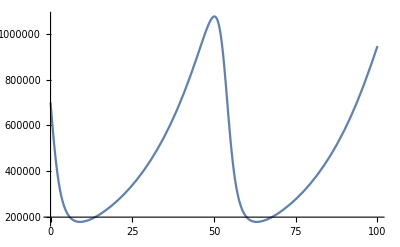

```mathematica
Plot[{Evaluate[k[t]/. sol]},{t,0,100},PlotRange->All]
```

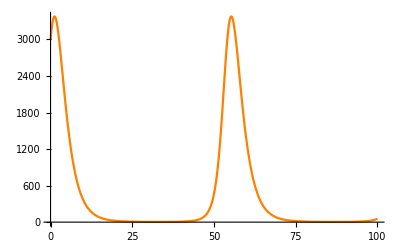

```mathematica
Plot[Evaluate[w[t]/. sol],{t,0,100},PlotRange->All, PlotStyle->Orange]
```

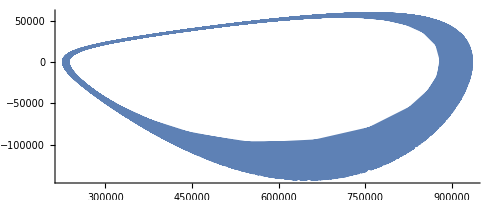

```mathematica
ParametricPlot[Evaluate[{k[t],k'[t]}/.sol],{t,0,10000},PlotRange->All]
```

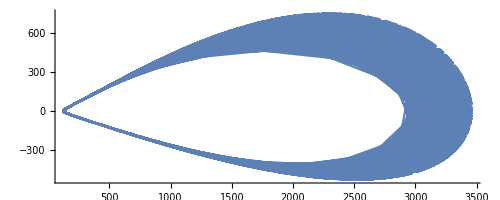

```mathematica
ParametricPlot[Evaluate[{w[t],w'[t]}/.sol],{t,0,10000},PlotRange->All]
```

```mathematica
Solve[0.2==0.0001*w1&&0.5==k1*0.000001&&0==(0.2-0.0001*w1)*k1&&0==(-0.5+0.000001*k1)*w1,{w1,k1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{w1→2000.,k1→500000.}}